# Name of Goblet

Names of groupmates

Class, Date

## Plots of functions

### Here is a space to practice plotting one function at a time.

Here we plot the function y=-3x+2 from x=0 to x=1.  Be careful with the format.

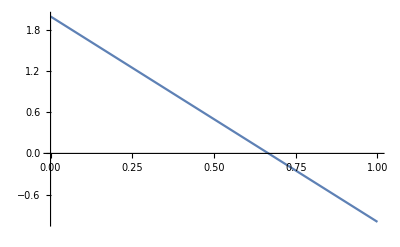

```mathematica
Plot[-3x+2,{x,0,1}]
```

### Here we have modified the window for showing this function

Here we are using the PlotRange option to override Mathematica’s default window.  We choose our window to be 0 <= x <= 10 and -2 <= y <= 2.

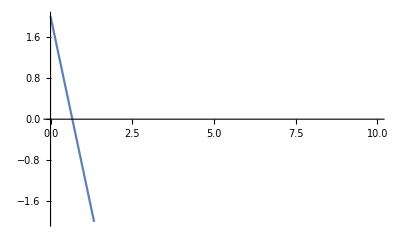

```mathematica
Plot[-3x+2,{x,0,2},PlotRange->{{0,10},{-2,2}}]
```

### Use the Show command to plot multiple functions at a time

After you have determined the functions that define the boundary of your goblet, you will want to show these plots on the same graph.  To do this, use the Show command.

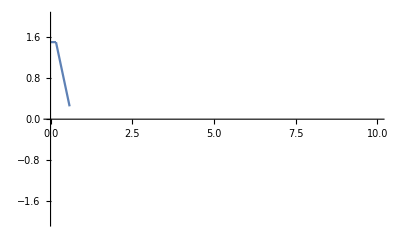

```mathematica
Show[{
Plot[1.5,{x,0,1/6},PlotRange->{{0,10},{-2,2}}],
Plot[-3x+2,{x,1/6,1.75/3},PlotRange->{{0,10},{-2,2}}]
}]
```

### Here is a plot of all the functions together

Here are all the parts together.  We have created the cross section of our goblet!

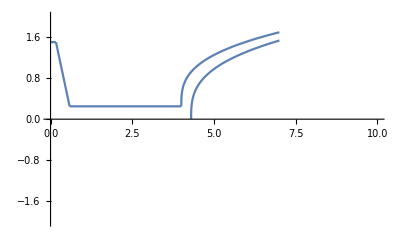

```mathematica
Show@{
Plot[1.5,{x,0,1/6},PlotRange->{{0,10},{-2,2}}],
Plot[-3x+2,{x,1/6,1.75/3},PlotRange->{{0,10},{-2,2}}],
Plot[0.25,{x,1.75/3,4},PlotRange->{{0,10},{-2,2}}],
Plot[(x-4)^(1/3)+.25,{x,4,7},PlotRange->{{0,10},{-2,2}}],
Plot[1.1(x-4.3)^(1/3),{x,4.3,7},PlotRange->{{0,10},{-2,2}}]
}
```

## Creating the piecewise defined functions

### We need to convert the functions from above to a piecewise-defined function

We want two piecewise-defined functions, one for the outer boundary and one for the inner boundary.  The format for each piece is a list {f(x),domain of x}.  Just copy the f(x) functions from above and modify the domains of x to be from the left boundary to the right boundary of each piece.

```mathematica
outer[x_]:=Piecewise[{
{1.5,0<=x<=1/6},
{-3x+2,1/6≤x<=1.75/3},
{0.25,1.75/3≤x≤4},
{(x-4)^(1/3)+.25,4≤x≤7}
}]
inner[x_]:=1.1(x-4.3)^(1/3);
```

### You can verify that your functions are correct!

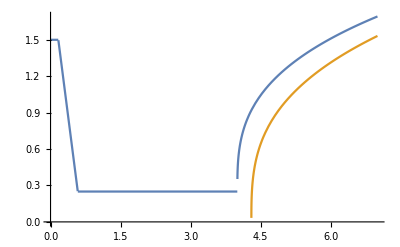

```mathematica
Plot[{outer[x],inner[x]},{x,0,7},PlotPoints->100]
```

## Creating the sides of the goblet

### Define the domains of the outer and inner functions. Ensure that the max x-value for each is the same!

```mathematica
outermin=0;
outermax=7;
innermin=4.3;
innermax=7;
```

### Define some parameters that are changeable

Define the number of points around the circle.

```mathematica
NumberOfSidesAround=100;
DeltaTheta=2Pi/NumberOfSidesAround;
```

Define the number of points along the outside of the goblet.

```mathematica
NumberOfPointsOutside=40;
DeltaOuter=(outermax-outermin)/NumberOfPointsOutside;
```

Define the number of points along the inside of the goblet.

```mathematica
NumberOfPointsInside=40;
DeltaInner=(innermax-innermin)/NumberOfPointsInside;
```

### The base is just a polygon.

```mathematica
base=Polygon[
Table[{0,outer[0]Cos[theta],-outer[0]Sin[theta]},{theta,0,2Pi,DeltaTheta}]
];
Graphics3D[base]
```

-Graphics3D-

### The lip is created by connecting a large number of quadrilaterals.

```mathematica
lip=Table[Polygon[{
{outermax,outer[outermax]Cos[theta],outer[outermax]Sin[theta]},{outermax,outer[outermax]Cos[theta+DeltaTheta],outer[outermax]Sin[theta+DeltaTheta]},
{innermax,inner[innermax]Cos[theta+DeltaTheta],inner[innermax]Sin[theta+DeltaTheta]},
{innermax,inner[innermax]Cos[theta],inner[innermax]Sin[theta]}}],
{theta,0,2Pi,DeltaTheta}];
Graphics3D[lip]
```

-Graphics3D-

### The inside of the goblet is created by connecting a large number of quadrilaterals

```mathematica
inside=Table[
Polygon[{
{x,inner[x]Cos[theta],inner[x]Sin[theta]},
{x+DeltaInner,inner[x+DeltaInner]Cos[theta],inner[x+DeltaInner]Sin[theta]},{x+DeltaInner,inner[x+DeltaInner]Cos[theta+DeltaTheta],inner[x+DeltaInner]Sin[theta+DeltaTheta]},{x,inner[x]Cos[theta+DeltaTheta],inner[x]Sin[theta+DeltaTheta]}
}],
{theta,0,2Pi,DeltaTheta},{x,innermin,innermax-DeltaInner/2,DeltaInner}];
Graphics3D[inside]
```

-Graphics3D-

### So is the outside!

```mathematica
outside=Table[
Polygon[{
{x,outer[x]Cos[theta],outer[x]Sin[theta]},
{x,outer[x]Cos[theta+DeltaTheta],outer[x]Sin[theta+DeltaTheta]},{x+DeltaOuter,outer[x+DeltaOuter]Cos[theta+DeltaTheta],outer[x+DeltaOuter]Sin[theta+DeltaTheta]},
{x+DeltaOuter,outer[x+DeltaOuter]Cos[theta],outer[x+DeltaOuter]Sin[theta]}}],
{theta,0,2Pi,DeltaTheta},{x,outermin,outermax-DeltaOuter,DeltaOuter}];
Graphics3D[outside]
```

-Graphics3D-

## Put it all together!

```mathematica
goblet=Graphics3D[{base,lip,inside,outside}]
```

-Graphics3D-

## Export the goblet

```mathematica
Export[NotebookDirectory[]<>"Goblet.stl",goblet]
```

/Users/chris/Downloads/Goblet.stl

```mathematica
SystemOpen[NotebookDirectory[]<>"Goblet.stl"]
```